## 数据

## 谷歌搜索算法

### 离散马尔可夫过程

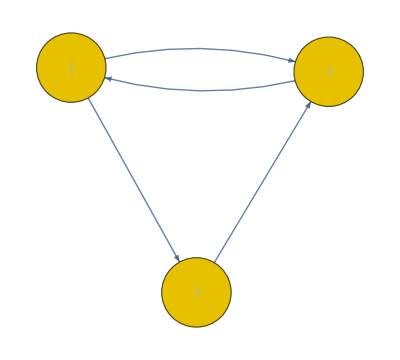

```mathematica
dmp=DiscreteMarkovProcess[{1/3,1/3,1/3},{{0,1/2,1/2},{0,0,1},{1,0,0}}];
Graph@dmp
```

```mathematica
StationaryDistribution[dmp]
```

ProbabilityDistribution[2/5 Boole[x==1]+1/5 Boole[x==2]+2/5 Boole[x==3],{x,1,3,1}]

### 线性代数

```mathematica
Limit[MatrixPower[{{0,1/2,1/2},{0,0,1},{1,0,0}},n],n->Infinity]
```

{{2/5,1/5,2/5},{2/5,1/5,2/5},{2/5,1/5,2/5}}

### 迭代计算

```mathematica
RSolveValue[{x[n+1]==z[n],y[n+1]==1/2x[n],z[n+1]==1/2x[n]+y[n],x[0]==1/3,y[0]==1/3,z[0]==1/3},{x[n],y[n],z[n]},n]//Limit[#,n->Infinity]&
```

{2/5,1/5,2/5}